```mathematica
ClearAll[line, files, importfile, raw, dataset, dataset1WithErrs]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/1.3/data3.xlsx}

```mathematica
importfile = files⟦1⟧
```

/Users/yaroslav/mipt/bachelor-3/semester-1/laboratory/1.3/data3.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
raw[[1]]
```

{{U,I},{0.019,0.2403},{-0.04,0.1931},{-0.077,0.1642},{-0.118,0.1323},{-0.15,0.1085},{-0.178,0.0883},{-0.216,0.0626},{-0.251,0.043},{-0.283,0.029},{-0.314,0.0185},{-0.354,0.0095},{-0.369,0.0075}}

```mathematica
table=Import[importfile]
```

{{{а,и},{6507.,0.0000289534},{6383.,0.0000295159},{6305.,0.000029881},{6217.,0.000030304},{6143.,0.0000306691},{6074.,0.0000310175},{5976.,0.0000315261},{5882.,0.0000320299},{5852.,0.0000321941},{5401.,0.0000348824}}}

```mathematica
table1=table[[1]]
```

{{6507.,0.0000289534,,,,,,},{6383.,0.0000295159,0.445,,,6383.,2.95159×10^15,0.445},{6305.,0.000029881,,,,6217.,3.0304×10^15,0.489},{6217.,0.000030304,0.489,,,6143.,3.06691×10^15,0.51},{6143.,0.0000306691,0.51,,,6074.,3.10175×10^15,0.526},{6074.,0.0000310175,0.526,,,5882.,3.20299×10^15,0.564},{5976.,0.0000315261,,,,5401.,3.48824×10^15,0.667},{5882.,0.0000320299,0.564,,,,,},{5852.,0.0000321941,,,,,,},{5401.,0.0000348824,0.667,,,,,},{\lambda, \AA,\omega, s,,,,,,},{,,,,,,,},{,,,,,,,},{,,,,,,,},{0.098909,,,1.6×10^-19,,,,},{,,,,,,,},{,,,,,,,},{,,,1.58254×10^-26,,,,}}

```mathematica
table1ᵀ
```

{{6507.,6383.,6305.,6217.,6143.,6074.,5976.,5882.,5852.,5401.,\lambda, \AA,,,,0.098909,,,},{0.0000289534,0.0000295159,0.000029881,0.000030304,0.0000306691,0.0000310175,0.0000315261,0.0000320299,0.0000321941,0.0000348824,\omega, s,,,,,,,},{,0.445,,0.489,0.51,0.526,,0.564,,0.667,,,,,,,,},{,,,,,,,,,,,,,,1.6×10^-19,,,1.58254×10^-26},{,,,,,,,,,,,,,,,,,},{,6383.,6217.,6143.,6074.,5882.,5401.,,,,,,,,,,,},{,2.95159×10^15,3.0304×10^15,3.06691×10^15,3.10175×10^15,3.20299×10^15,3.48824×10^15,,,,,,,,,,,},{,0.445,0.489,0.51,0.526,0.564,0.667,,,,,,,,,,,}}

## Dataset

```mathematica
dataset=makeDataset[raw⟦1⟧]
```

```mathematica
dataset1WithErrs=dataset[All,<|"w"->(-Log[#I]+0.621651&),"U"->(#U&)|>]
```

```mathematica
dataset2WithErrs=dataset1WithErrs[All,<|"b"->(#b&),"h1"->(#h1&),"h2"->(#h2&),"h3"->(#h3&),"h4"->(#h4&),"v"->((#h4-#h3)/(#h4+#h3)&),"d"->((#h1)/(#h2)&)|>]
```

```mathematica
dataset3WithErrs=dataset2WithErrs[All,<|"b"->(#b&),"h1"->(#h1&),"h2"->(#h2&),"h3"->(#h3&),"h4"->(#h4&),"v"->(#v&),"d"->(#d&),
"v1"->((2 √(#d))/(#d+1)&)|>]
```

```mathematica
dataset4WithErrs=dataset3WithErrs[All,<|"b"->(#b&),"h1"->(#h1&),"h2"->(#h2&),"h3"->(#h3&),"h4"->(#h4&),"v"->(#v&),"d"->(#d&),
"v1"->(#v1&),"v3"->((#v)/(#v1)&)|>]
```

```mathematica
dataset5WithErrs=dataset4WithErrs[All,<|"b"->(#b-110&),"h1"->(#h1&),"h2"->(#h2&),"h3"->(#h3&),"h4"->(#h4&),"v"->(#v&),"d"->(#d&),
"v1"->(#v1&),"v3"->(#v3&)|>]
```

```mathematica
dataset6WithErrs=dataset5WithErrs[All,<|"b"->(#b&),"v3"->(#v3&)|>]
```

```mathematica
dataset2WithErrs=dataset1WithErrs[All,<|"U"->(#U["Value"]&),"dU"->(#U["Uncertainty"]&),"I"->(#I["Value"]&),"dI"->(#I["Uncertainty"]&)|>]
```

```mathematica
dataset2=dataset2WithErrs[[Values]]
```

```mathematica
Normal[dataset2WithErrs[All,{"U","I"}/*Values]]
```

```mathematica
hi={{-0.019,0.48249352327259276},{0.04,0.4308131845707603},{0.077,0.39585350825778975},{0.118,0.35327043465311386},{0.15,0.3178049716414141},{0.178,0.28425340807103794},{0.216,0.23473389188611005},{0.251,0.18841443681416772},{0.283,0.1466287829861518},{0.314,0.10488088481701516},{0.354,0.044721359549995794},{0.369,0}}
```

{{-0.019,0.482494},{0.04,0.430813},{0.077,0.395854},{0.118,0.35327},{0.15,0.317805},{0.178,0.284253},{0.216,0.234734},{0.251,0.188414},{0.283,0.146629},{0.314,0.104881},{0.354,0.0447214},{0.369,0}}

```mathematica
line=LinearModelFit[hi,{1,x},x]
```

FittedModel[0.487636-1.23027 x]

```mathematica
Around[0.487,.009]/Around[1.23,0.04]
```

0.3960.015

```mathematica
Around[0.487,0.009]/Around[1.23,0.04]
```

Syntax::sntxf: "Around[" cannot be followed by "1.23 ,0.04]".

```mathematica
Export["/Users/yaroslav/Desktop/dataset.csv",dataset2]
```

/Users/yaroslav/Desktop/dataset.csv

```mathematica
line =LinearModelFit[Normal@dataset[All,{"n","T"}/*Values],{1,x},x]
```

FittedModel[0.00692389+0.212328 x]

```mathematica
line["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.487636 | 0.00945369 | 51.5816 | 1.8142×10^-13
x | -1.23027 | 0.041397 | -29.719 | 4.34864×10^-11

```mathematica
Normal@line
```

0.00692389+0.212328 x

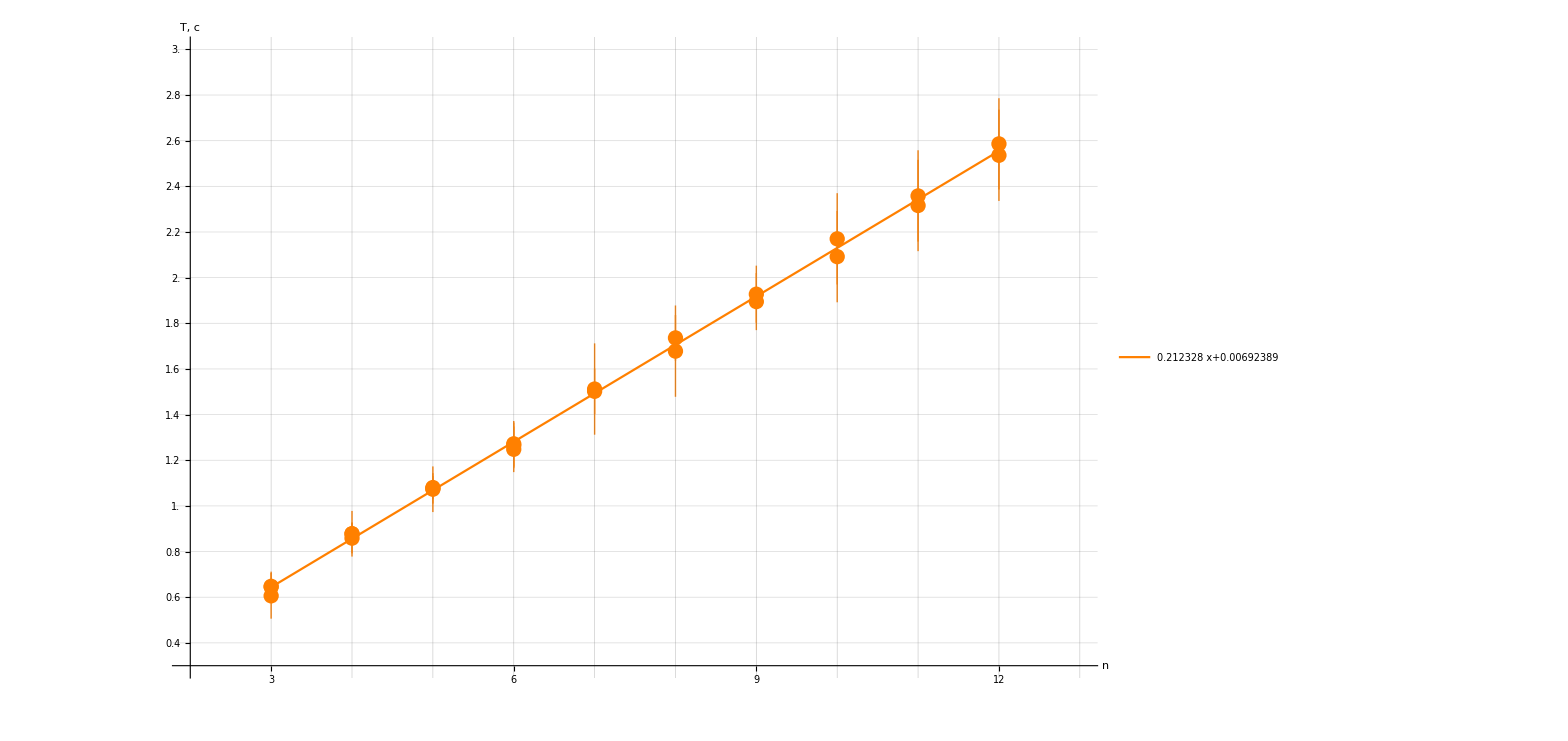

```mathematica
Show[
Plot[
{line@x},
{x,3, 12},
AxesLabel->{Style["n", Large],Style["T, c",Large]},
ImageSize->1200,
AxesStyle->Directive[Arrowheads[{0.02}],Black],
GridLines-> {Range[0,15,1],Range[0,10,0.1]},
PlotRange->{{2,13},{0.3,3.}},
Ticks-> {Range[0,50,1],Range[0,3,0.2]},
TicksStyle->15,
PlotStyle->Orange,
PlotLegends->Placed[
LineLegend[
{Normal@line},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
]
],
ListPlot[
{dataset1WithErrs},
PlotStyle->Orange
]
]
```

```mathematica
ClearAll[line, files, importfile, raw, dataset, dataset1WithErrs]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/3 семестр/121/data2.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр/121/data.xlsx,/Users/leonidbarinov/Desktop/latexlabs/3 семестр/121/~$data2.xlsx}

```mathematica
importfile = files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/3 семестр/121/data2.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
dataset2=makeDataset[raw⟦1⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"n"->(#n&),"M"->(Around[#M,#dm]&)|>]
```

Dataset[<>]

```mathematica
line2 =LinearModelFit[Normal@dataset2[All,{"n","M"}/*Values],{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+37.7518 x]

```mathematica
line=LinearModelFit[{{2.951590161366129*^15,0.445},{3.0304005147177095*^15,0.489},{3.0669054208041675*^15,0.51},{3.101745143233454*^15,0.526},{3.202992179530772*^15,0.564},{3.488242917978152*^15,0.667}},{1,x},x]
```

FittedModel[-0.72516+4.00807×10^-16 x]

```mathematica
{{2.951590161366129*^15,3.0304005147177095*^15,3.0669054208041675*^15,3.101745143233454*^15,3.202992179530772*^15,3.488242917978152*^15},Around[{0.445,0.489,0.51,0.526,0.564,0.667},0.005]}ᵀ
```

{{2.95159×10^15,0.4450.005},{3.0304×10^15,0.4890.005},{3.06691×10^15,0.5100.005},{3.10175×10^15,0.5260.005},{3.20299×10^15,0.5640.005},{3.48824×10^15,0.6670.005}}

```mathematica
line["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.72516 | 0.0672416 | -10.7844 | 0.000419252
x | 4.00807×10^-16 | 2.138×10^-17 | 18.7468 | 0.0000476699

```mathematica
Show[Plot[-0.7251596840742605+4.0080711544439106*^-16 x,{x,2.951590161366129*^15,3.488242917978152*^15}],ListPlot[{{2.951590161366129*^15,3.0304005147177095*^15,3.0669054208041675*^15,3.101745143233454*^15,3.202992179530772*^15,3.488242917978152*^15},Around[{0.445,0.489,0.51,0.526,0.564,0.667},0.007]}ᵀ]]
```

-Graphics-

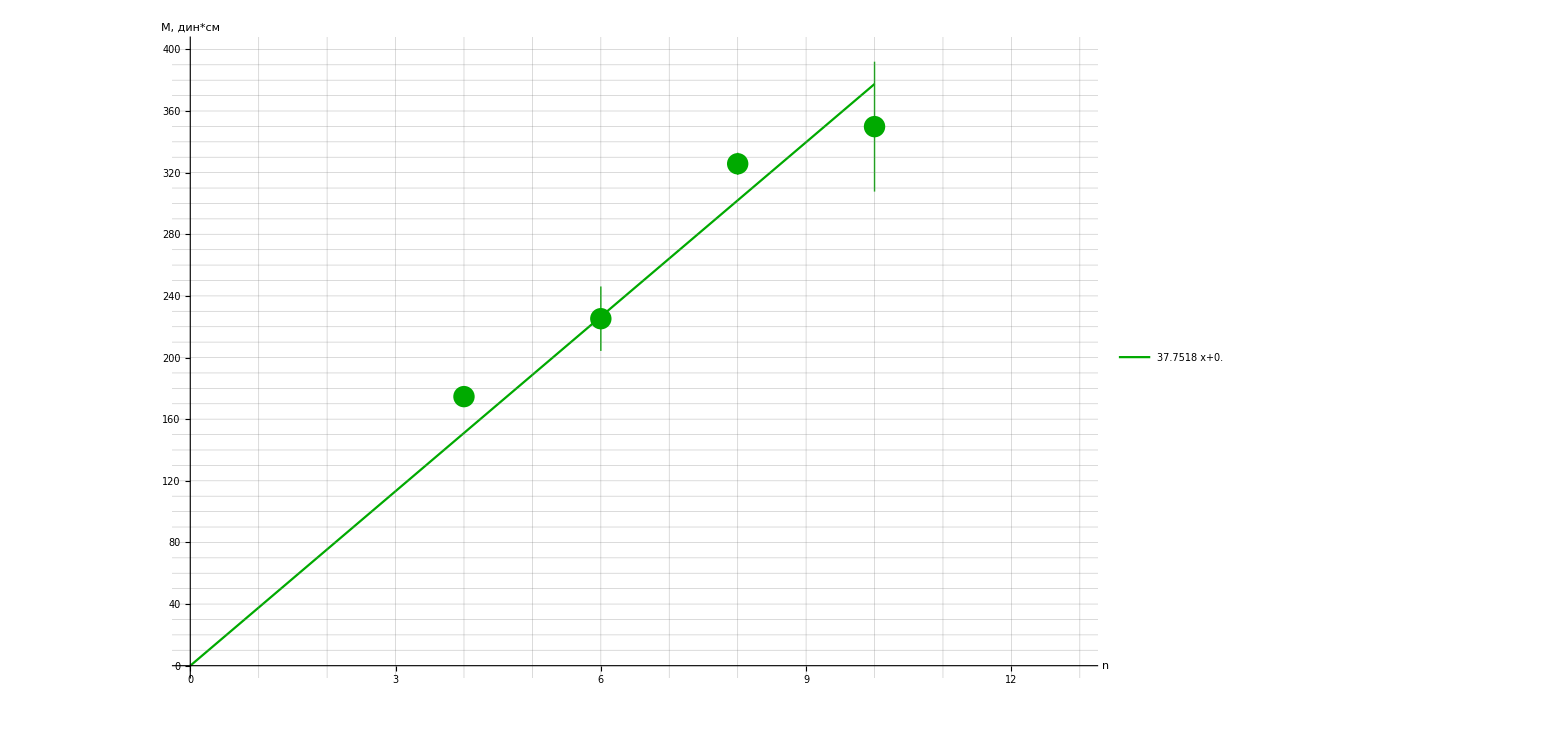

```mathematica
Show[
Plot[
{line2@x},
{x,0, 10},
AxesLabel->{Style["n", Large],Style["M, дин*см",Large]},
ImageSize->1200,
AxesStyle->Directive[Arrowheads[{0.02}],Black],
GridLines-> {Range[0,15,1],Range[0,400,10]},
PlotRange->{{0,13},{0,400}},
Ticks-> {Range[0,50,1],Range[0,400,20]},
TicksStyle->15,
PlotStyle->Darker[Green],
PlotLegends->Placed[
LineLegend[
{Normal@line2},
LabelStyle->20
],
{Scaled[0.2],Scaled[0.75]}
]
],
ListPlot[
{dataset2WithErrs},
PlotStyle->Darker[Green]
]
]
```

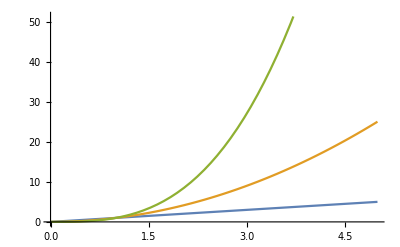

```mathematica
Plot[{x,x^2,x^3},{x,0,5}]
```

```mathematica
m=({{10, 4, 5+10p1+4p2}, {4, -2, -1+4p1-2p2}, {5+10p1+4p2, -1+4p1-2p2, 0}})
```

{{10,4,5+10 p1+4 p2},{4,-2,-1+4 p1-2 p2},{5+10 p1+4 p2,-1+4 p1-2 p2,0}}

```mathematica
Det[m]
```

360 p1+360 p1^2-72 p2+288 p1 p2-72 p2^2

```mathematica
Simplify[360 p1+360 p1^2-72 p2+288 p1 p2-72 p2^2]
```

72 (5 p1^2-p2 (1+p2)+p1 (5+4 p2))

```mathematica
dataset=makeDataset[raw⟦4⟧]
```

```mathematica
dataset1WithErrs=dataset[All,<|"l"->(Around[#l,0.1]&),"h1"->(Around[#h1,1.0]&),"h2"->(Around[#h2,1.0]&),"h3"->(Around[#h3,1.0]&),"h4"->(Around[#h4,1.0]&)|>]
```

```mathematica
dataset2WithErrs=dataset1WithErrs[All,<|"l"->(#l&),"h1"->(#h1&),"h2"->(#h2&),"h3"->(#h3&),"h4"->(#h4&),"v"->((#h4-#h3)/(#h4+#h3)&),"d"->((#h1)/(#h2)&)|>]
```

```mathematica
dataset3WithErrs=dataset2WithErrs[All,<|"l"->(#l&),"h1"->(#h1&),"h2"->(#h2&),"h3"->(#h3&),"h4"->(#h4&),"v"->(#v&),"d"->(#d&),
"v1"->((2 √(#d))/(#d+1)&)|>]
```

```mathematica
dataset4WithErrs=dataset3WithErrs[All,<|"l"->(#l&),"h1"->(#h1&),"h2"->(#h2&),"h3"->(#h3&),"h4"->(#h4&),"v"->(#v&),"d"->(#d&),
"v1"->(#v1&),"v2"->((#v)/(#v1)&)|>]
```

```mathematica
dataset5WithErrs=dataset4WithErrs[All,<|"l"->(#l&),"h1"->(#h1&),"h2"->(#h2&),"h3"->(#h3&),"h4"->(#h4&),"v"->(#v&),"d"->(#d&),
"v1"->(#v1&),"v2"->(#v2&)|>]
```

```mathematica
dataset6WithErrs=dataset5WithErrs[All,<|"l"->(#l&),"v2"->(#v2&)|>]
```

```mathematica
dataset7WithErrs=dataset6WithErrs[All,<|"l"->(#l["Value"]&),"dl"->(#l["Uncertainty"]&),"v2"->(#v2["Value"]&),"dv2"->(#v2["Uncertainty"]&)|>]
```

```mathematica
Export["dataset.csv",dataset1WithErrs]
```

dataset.csv

```mathematica
SystemOpen["dataset.csv"]
```

```mathematica
SystemOpen["dataset.csv"]
```

```mathematica
SystemOpen["dataset.csv"]
```

```mathematica
SystemOpen["dataset.csv"]
```

```mathematica
0.26*3*10^8/Around[0.07,0.07]
```

1.11.110^9

```mathematica
1+(2 Around[1.1,1.1] 10^9)/(Around[4.9,0.9] 10^8)
```

5.5.

```mathematica
3* 110 10^-3
```

33/100

```mathematica
N[33/100]
```

```mathematica
26/0.33
```

```mathematica
78.78787878787878*3/4
```

59.0909

```mathematica
N[77/25000]
```

0.00308

```mathematica
table={2π *3*10^8/({6507,6334,6164,6030,5976,5882,5401}*10^-10),{0.368,0.416,0.464,0.507,0.521,0.553,0.710}}
```

{{(2000000000000000000 π)/2169,(3000000000000000000 π)/3167,(1500000000000000000 π)/1541,(200000000000000000 π)/201,(250000000000000000 π)/249,(3000000000000000000 π)/2941,(6000000000000000000 π)/5401},{0.368,0.416,0.464,0.507,0.521,0.553,0.71}}

```mathematica
ntab=N[tableᵀ]
```

{{2.89681×10^15,0.368},{2.97593×10^15,0.416},{3.05801×10^15,0.464},{3.12596×10^15,0.507},{3.15421×10^15,0.521},{3.20462×10^15,0.553},{3.49001×10^15,0.71}}

```mathematica
ListPlot[tableᵀ]
```

-Graphics-

```mathematica
fit=LinearModelFit[tableᵀ,{1,x},x]
```

FittedModel[-1.29967+5.7687×10^-16 x]

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.29967 | 0.022193 | -58.562 | 2.74706×10^-8
x | 5.7687×10^-16 | 7.08055×10^-18 | 81.4726 | 5.27893×10^-9

```mathematica
Around[-1.30,0.02]/(Around[5.77,0.07]*10^-16)
```

-2.250.0410^15

```mathematica
(2π *3*10^8)/(-2.250.0410^15)
```

```mathematica
-8.370.1610^-7* 10^10
```

-8366.164.

```mathematica
Around[0.921,0.011]* 10^-34*-2.250.0410^15
```

```mathematica
-2.080.0510^-19/(1.602 *10^-19)
```

-1.2950.030

```mathematica
Export["dataset.csv",ntab]
```

dataset.csv

```mathematica
SystemOpen["dataset.csv"]
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
dataset=makeAssoc[{a,b}][ntabᵀ]//Dataset
```

```mathematica
dataset=makeDataset[hi]
```

```mathematica
ntabᵀ
```

```mathematica
{{2.8968120365051115*^15,2.975932415778143*^15,3.0580071254929845*^15,3.125962839392829*^15,3.154209491556017*^15,3.204616783668609*^15,3.4900122054320975*^15}/10^15,{0.368,0.416,0.464,0.507,0.521,0.553,0.71}}
```

```mathematica
{{2.8968120365051115,2.9759324157781433,3.058007125492985,3.1259628393928294,3.154209491556017,3.2046167836686092,3.4900122054320977},{0.368,0.416,0.464,0.507,0.521,0.553,0.71}}ᵀ
```

{{2.89681,0.368},{2.97593,0.416},{3.05801,0.464},{3.12596,0.507},{3.15421,0.521},{3.20462,0.553},{3.49001,0.71}}

```mathematica
hi={{"x","y"},{2.8968120365051115*^15,0.368},{2.975932415778143*^15,0.416},{3.0580071254929845*^15,0.464},{3.125962839392829*^15,0.507},{3.154209491556017*^15,0.521},{3.204616783668609*^15,0.553},{3.4900122054320975*^15,0.71}}
```

```mathematica
hi={{"x","y"},{2.8968120365051115,0.368},{2.9759324157781433,0.416},{3.058007125492985,0.464},{3.1259628393928294,0.507},{3.154209491556017,0.521},{3.2046167836686092,0.553},{3.4900122054320977,0.71}}
```

{{x,y},{2.89681,0.368},{2.97593,0.416},{3.05801,0.464},{3.12596,0.507},{3.15421,0.521},{3.20462,0.553},{3.49001,0.71}}

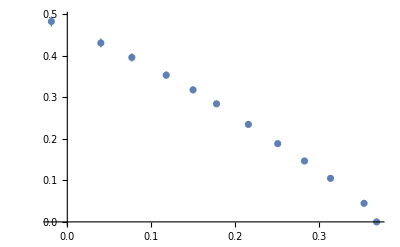

```mathematica
ListPlot[dataset1WithErrs]
```

```mathematica
6.62607015/(2 π)
```

1.05457